```mathematica
Needs["PlotLegends`"]
Directory[]
```

C:\Documents and Settings\Administrator\My Documents

{Real,Real,Real,Real,Real,Real,Real,Real,Real,Real}

10

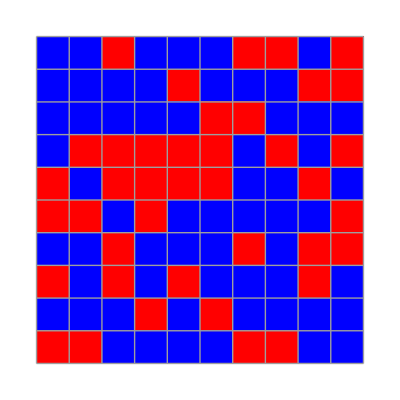

```mathematica
type=Table[Real,{k,1,10}]
data=ReadList["one.txt",type];
nn=Dimensions[data][[1]]
ArrayPlot[data,ColorRules->{1.0->Blue,-1.0->Red},Mesh->True]
data;
```

{Real,Real}

550

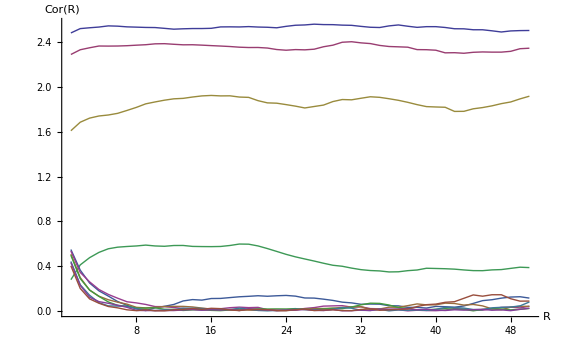

```mathematica
type=Table[Real,{k,1,2}]
data=ReadList["out2dcor.txt",type];
nn=Dimensions[data][[1]]
ListLinePlot[Table[Table[{data[[k]][[1]],data[[k]][[2]]},{k,1+(k2-1)*50,50+(k2-1)*50}],{k2,1,11}],AxesLabel->{"R","Cor(R)"},PlotRange->Full]
```

{Real,Real,Real,Real,Real}

101

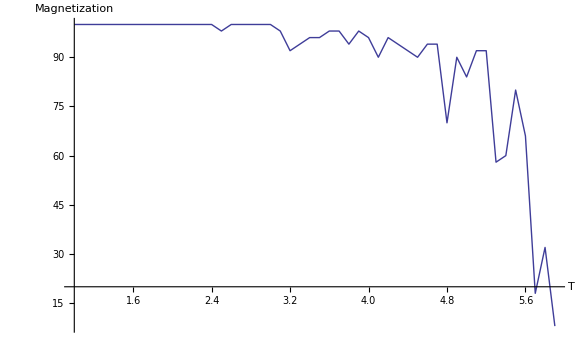

```mathematica
type=Table[Real,{k,1,5}]
data=ReadList["out4.txt",type];
nn=Dimensions[data][[1]]
ListLinePlot[Table[{data[[k]][[1]],data[[k]][[5]]},{k,1,50}],AxesLabel->{"T","Magnetization"},PlotRange->Full]
```